# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu_develop"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
(* time and duration unit μs: 300 ms*)
T1-><|"Alice"->3*10^5, "Bob"->3*10^5    |>,
(* Simulating T2* error by gaussian decay: 10 ms *)
T2s-><|"Alice"->10^4,  "Bob"->10^4   |>,
(* Switch on/off the standard passive noise: Amplitude damping T1 and dephasing T2  *)
StdPassiveNoise->True,
(* Duration for moving operations: Split, Combine, and physical swap; they have zero error *)
DurMove-><|"Alice"-> <|Shutl->10, Splz->50, Comb->50, SWAPLoc->10 |>,"Bob"-><|Shutl->10, Splz->50, Comb->50, SWAPLoc->10 |>|>,
(* fidelity of preparation/initialisation; initialisation is done by amplitude damping *)
FidInit-><|"Alice"->0.9999, "Bob"->0.9998|>,
DurInit-><|"Alice"->20,"Bob"->20|>,

(* Readout error includes bitflip and scattering
Bitflip error represents symmetric error on both 0 and 1 readout  
Amplitude damping represents scattering error affecting the neighborhood qubits (in the same zone): collapsing the superposition into 0
*)
DurRead-><|"Alice"->20, "Bob"->20|>,
BFProb-><|"Alice"->10^-3,"Bob"->10^-3|>,
ScatProb-><|"Alice"->0.05, "Bob"->0.05|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone*)
FidSingleXY-><|"Alice"->0.99999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{0,1},"Bob"->{0,1}|>,

(* Frequency unit is MHz *)
(* Rabi frequency on single rotations in MHz  *)
RabiFreq-><|"Alice"->1, "Bob"->1 |>,
(* Frequency of CZ operation*)
FreqCZ-><|"Alice"->0.1,"Bob"->0.1|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.999, "Bob"->0.999|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{1,0}|>,
(* frequency of remote entanglement MHz *)
FreqEnt->100*10^3,
(* fidelity of remote entanglement *)
FidEnt->0.985,
(* fraction of noise: depolarizing:dephasing *)
EFEnt->{0,1}
};
```

Commonly defined standard gates that can be easily composed to the native Trapped ion gates , chart style

```mathematica
StdGates::usage="Replacements for standard gates that are straightforwardly composable to the native trapped ions gates. Here, hadamard is implemented with π/2-rotation around";
StdGates={Subscript[H, q_][n_]:>Sequence@@{Subscript[Rx, q][n,π/2]}};
```

```mathematica
chartstyle[label_]:={ImageSize->400,BarSpacing->0.1,ColorFunction->Function[{height},If[height<0.1,ColorData["Rainbow"][10height],ColorData["DeepSeaColors"][(height-0.9)*10]]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},Automatic},LabelStyle->Directive[Bold,Black],
Epilog->Inset[Style[label,Thick,17],ImageScaled[{.2,.7}]],PlotRange->All
};
```

[Native Gates]
 Init_q[node], Read_q[node], Rx_q[node,θ], Ry_q[node,θ], CZ_(q1,q2)[node], Ent[node1, node2], SWAPLoc_(q1,q2)[node], Splz_(q1,q2)[node,zone_destination], Comb_(q1,q2)[node], Comb_(q1,q2)[node,zone_destination]

[Zone and operations]
[from notes]
Zone 1 : prepare, store?, detect
Zone 2 : prepare, store?, detect, logic
Zone 3 : prepare, store?, detect, logic
Zone 4 : remote entangle
[from email]
    a. Zone 1 supports prep, detect, split, combine and rotate (SWAP), but
        no local or remote quantum logic
     b. Zone 2 and 3 are as (a) plus local logic (1Q and 2Q) only
     c. Zone 4 supports remote logic only (no split, combine, rotate?)

The device initialised with a connected ions in the zone 1.

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["~/vqd/img/tions.pdf",%]
```

~/vqd/img/tions.pdf

The total circuit and moves until page 38. The expected result is qubit 4 at zone 2 is highly entangled after 3 distillations .

```mathematica
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"],Subscript[Comb, 2,4]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Splz, 4,2]["Alice",3],Subscript[Splz, 4,2]["Bob",3],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 2,3]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],
Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 3,2]["Bob"],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 3,2]["Bob",2],Subscript[Comb, 4,3]["Alice"],Subscript[CZ, 4,3]["Alice"],Subscript[Comb, 4,3]["Bob"],Subscript[CZ, 4,3]["Bob"],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"],Subscript[H, 4]["Alice"],Subscript[H, 3]["Alice"],Subscript[H, 3]["Bob"],Subscript[H, 4]["Bob"],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Splz, 4,3]["Alice",3],Subscript[Splz, 4,3]["Bob",3]
}/.StdGates;
```

Check the arrangement of the circuit in the total density matrix. Here is completely serial within a node.
 It does not update the device state, thus we cannot check the final position of ions.

```mathematica
(*DrawCircuit@CircTrappedIons[circ,dev]*)
```

This will show the total scheduling, noise operation, and the final form in the simulation.
Set the MapQubits->False and ReplaceAliases->True if you intended to do the density matrix simulation

```mathematica
Options@TrappedIonOxford
```

{Nodes→<|Alice→4,Bob→4|>,T1→<|Alice→300000,Bob→300000|>,T2s→<|Alice→10000,Bob→10000|>,StdPassiveNoise→True,DurMove→<|Alice→<|Shutl→10,Splz→50,Comb→50,SWAPLoc→10|>,Bob→<|Shutl→10,Splz→50,Comb→50,SWAPLoc→10|>|>,FidInit→<|Alice→0.9999,Bob→0.9998|>,DurInit→<|Alice→20,Bob→20|>,DurRead→<|Alice→20,Bob→20|>,BFProb→<|Alice→1/1000,Bob→1/1000|>,ScatProb→<|Alice→0.05,Bob→0.05|>,FidSingleXY→<|Alice→0.99999,Bob→0.99999|>,EFSingleXY→<|Alice→{0,1},Bob→{0,1}|>,RabiFreq→<|Alice→1,Bob→1|>,FreqCZ→<|Alice→0.1,Bob→0.1|>,FidCZ→<|Alice→0.999,Bob→0.999|>,EFCZ→<|Alice→{1,0},Bob→{1,0}|>,FreqEnt→100000,FidEnt→0.985,EFEnt→{0,1}}

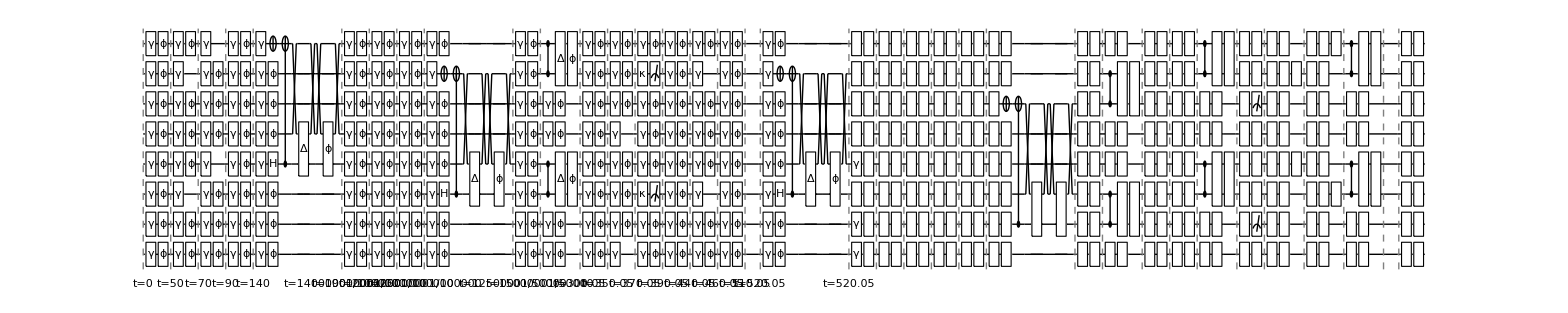

```mathematica
dev=TrappedIonOxford[];
circ2=CircTrappedIons[circ,dev,MapQubits->False];
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
DrawCircuit[%,8]
```

```mathematica
(* initialise the qubit with random mixed state, then apply the noisy circuit *)
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
SetQuregMatrix[ρ,RandomMixState[8]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
ApplyCircuit[InitZeroState@ψ2,{Subscript[H, 0],Subscript[C, 0][Subscript[X, 1]]}];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,4,5,6]];
CalcFidelity[ρ2,ψ2]
PlotDensityMatrix[PartialTrace[ρ,0,1,2,4,5,6],ψ2,Sequence@@chartstyle[""]]
```

0.967421

-Graphics3D-

Recall the expected result is qubit 4 at zone 2 is highly entangled after 3 distillations: trace out the rest except qubit 4 at both nodes. Thus we trace out the rest of other qubits above.

```mathematica
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

[FUTURE FEATURES]

T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
ModifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.
Passive noise different on each zone.
The noise on the move operations? (passive noise)
Correlated noise happens only to qubits with the same zone.
The role of measurement/outcome in the sequence?
Measurement involves scattering that can affect neighborhood atoms within raidus.
Parrallel -> False (done), Default (no operations in the same zone, always parallel Alice and Bob, Ent is always serial) , Full (Default+ parallel when in different zone)

## Entanglement distillation against dephasing noise

In the case when entanglement has only dephasing errors, one-round of distillation is sufficient.

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[4];
ψ=CreateQureg[4];
ρ2=CreateDensityQureg[2];
ψ2=CreateQureg[2];
```

```mathematica
Subscript[bell, p_,q_]:=Sequence@@{Subscript[H, p],Subscript[X, q],Subscript[C, p][Subscript[X, q]]}
Subscript[belle, p_,q_][err_]:=Sequence@@{Subscript[bell, p,q],Subscript[Deph, p,q][1-fidEnt]}
distill[n_]:=Flatten@{Subscript[bellerr, 0,2][1-fidEnt],ConstantArray[{Subscript[bellerr, 1,3][1-fidEnt],Subscript[H, 0],Subscript[H, 1],Subscript[H, 2],Subscript[H, 3],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 2][Subscript[X, 3]],Subscript[Rx, 2][π],Subscript[M, 1],Subscript[M, 3]},n-1]};
gatereplace={Subscript[H, q_]:>Sequence@@{Subscript[Ry, q][π/2],Subscript[Rx, q][-π]},Subscript[bellerr, p_,q_][e_]:>Subscript[belle, p,q][e]};
```

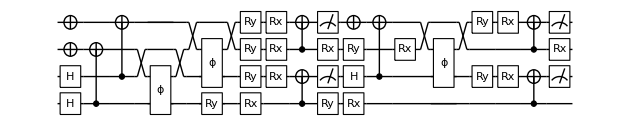

```mathematica
DrawCircuit[distill[3]/.gatereplace]
```

Ntrial=5 Fidelity=1.

output:{{1,0.985},{2,0.999898},{3,0.999898},{4,0.999898},{5,0.999999},{6,0.999999},{7,0.999999},{8,1.},{9,1.},{10,1.}}

-Graphics3D-

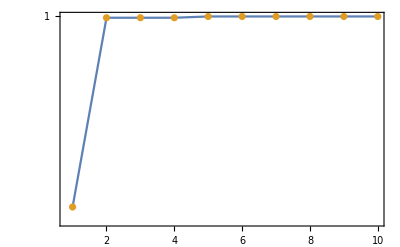

```mathematica
fidEnt=0.985; (* entanglement fidelity *)
nrounds=10; (* the total rounds of distillation *)

output={{1,fidEnt}};
ApplyCircuit[InitZeroState@ψ2,{Subscript[bell, 0,1]}];
Table[
trial=0;
While[trial<5,
trial++;
out=Flatten@ApplyCircuit[InitZeroState@ρ,distill[n]/.gatereplace];
If[AllTrue[out,#==0&] (* omit output 11, avodiing correction XX *),
SetQuregMatrix[ρ2,PartialTrace[ρ,1,3]];
Break[]]
];
AppendTo[output,{n,CalcFidelity[ρ2,ψ2]}]
,{n,2,nrounds}];
Print["Ntrial=",trial," Fidelity=",CalcFidelity[ρ2,ψ2]]
Print["output:",output]
PlotDensityMatrix[ρ2,ψ2,Sequence@@chartstyle[""]]
ListLogPlot[{output,output},Joined->{True,False},PlotTheme->"Detailed",PlotRange->All]
```

## Implementation on the trapped ions

Zone 1 : prepare, store?, detect
Zone 2 : prepare, store?, detect, logic
Zone 3 : prepare, store?, detect, logic
Zone 4 : remote entangle

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
DestroyAllQuregs[]
ρ=CreateDensityQureg[8];
ρ2=CreateDensityQureg[2];
ψ2=CreateQureg[2];
ρinit=CreateDensityQureg[8];
ApplyCircuit[ψ2,{Subscript[bell, 0,1]}];
```

```mathematica
ρ22=CreateDensityQureg[2];
```

```mathematica
SetQuregMatrix[ρinit,RandomMixState[8]];
```

One round of entanglement distillation

```mathematica
CircTrappedIons[circ,dev,MapQubits->False]
```

{{Splz_(2,3)[Alice,3],Splz_(2,3)[Bob,3]},{Init_3[Alice],Init_3[Bob]},{Init_4[Alice],Init_4[Bob]},{Splz_(3,4)[Alice,4],Splz_(3,4)[Bob,4]},{Ent_(4,4)[Alice,Bob]},{Comb_(3,4)[Alice,3],Comb_(3,4)[Bob,3]},{SWAPLoc_(3,4)[Alice],SWAPLoc_(3,4)[Bob]},{Splz_(4,3)[Alice,4],Splz_(4,3)[Bob,4]},{Ent_(3,3)[Alice,Bob]},{Comb_(4,3)[Alice,3],Comb_(4,3)[Bob,3]},{CZ_(4,3)[Alice],CZ_(4,3)[Bob]},{Splz_(4,3)[Alice,2],Splz_(4,3)[Bob,2]},{Init_1[Alice],Init_1[Bob]},{Read_3[Alice],Read_3[Bob]},{Splz_(1,2)[Alice,2],Splz_(1,2)[Bob,2]},{Init_3[Alice],Init_3[Bob]},{Comb_(2,4)[Alice],Comb_(2,4)[Bob]},{Shutl_3[Alice,4],Shutl_3[Bob,4]},{Ent_(3,3)[Alice,Bob]},{SWAPLoc_(2,4)[Alice],SWAPLoc_(2,4)[Bob]},{Splz_(4,2)[Alice,3],Splz_(4,2)[Bob,3]},{Comb_(2,3)[Alice,3],Comb_(2,3)[Bob,3]},{SWAPLoc_(2,3)[Alice],SWAPLoc_(2,3)[Bob]},{Splz_(3,2)[Alice,4],Splz_(3,2)[Bob,4]},{Ent_(2,2)[Alice,Bob]},{Comb_(3,2)[Alice,3],Comb_(3,2)[Bob,3]},{CZ_(3,2)[Alice],CZ_(3,2)[Bob]},{Splz_(3,2)[Alice,2],Splz_(3,2)[Bob,2]},{Comb_(4,3)[Alice],Comb_(4,3)[Bob]},{CZ_(4,3)[Alice],CZ_(4,3)[Bob]},{Read_2[Alice],Read_2[Bob]},{Rx_4[Alice,π/2],Rx_3[Bob,π/2]},{Rx_3[Alice,π/2],Rx_4[Bob,π/2]},{CZ_(4,3)[Alice],CZ_(4,3)[Bob]},{Shutl_2[Alice,4],Shutl_2[Bob,4]},{Splz_(4,3)[Alice,3],Splz_(4,3)[Bob,3]}}

```mathematica
dev=TrappedIonOxford[];
circ={Subscript[Splz, 3,4]["Alice",3],Subscript[Splz, 3,4]["Bob",3],Subscript[Init, 4]["Alice"],Subscript[Init, 4]["Bob"],Subscript[Shutl, 4]["Alice",4],Subscript[Shutl, 4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"]};
circ2=CircTrappedIons[circ,dev,MapQubits->False]
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
dev[ShowNodes]
CloneQureg[ρ,ρinit];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
SetQuregMatrix[ρ22,PartialTrace[ρ,0,1,2,4,5,6]];
CalcFidelity[ρ22,ψ2]
```

{{Splz_(3,4)[Alice,3],Splz_(3,4)[Bob,3]},{Init_4[Alice],Init_4[Bob]},{Shutl_4[Alice,4],Shutl_4[Bob,4]},{Ent_(4,4)[Alice,Bob]}}

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

0.9875

```mathematica
GetQuregMatrix@ρ22
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.5+0. ⅈ,0.4875+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.4875+0. ⅈ,0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
chartstyle[""]
```

{ImageSize→400,BarSpacing→0.1,ColorFunction→Function[{height},If[height<0.1,ColorData[Rainbow][10 height],ColorData[DeepSeaColors][(height-0.9) 10]]],ChartElementFunction→Cube,ChartStyle→EdgeForm[Thickness[Large]],PlotTheme→Business,Ticks→{{{1,00},{2,01},{3,10},{4,11}},{{1,00},{2,01},{3,10},{4,11}},Automatic},LabelStyle→Directive[Bold,GrayLevel[0]],Epilog→Inset[,ImageScaled[{0.2,0.7}]],PlotRange→All}

```mathematica
PlotDensityMatrix[ρ22,ψ2,PlotRange->{{1,4},{1,4},{0,0.5}},Sequence@@chartstyle["F=98.75\n round 1"]]
```

-Graphics3D-

Two rounds of entanglement distillation

```mathematica
DeleteCases[SimplifyCircuit[distill[2]/.{Subscript[C, p_][Subscript[X, q_]]:>Sequence@@{Subscript[H, q],Subscript[CZ, p,q],Subscript[H, q]}}],G[_]]/.{Subscript[H, q_]:>{Subscript[Ry, q][π/2],Subscript[Rx, q][-π]}}
```

{bellerr_(0,2)[0.015],bellerr_(1,3)[0.015],{Ry_0[π/2],Rx_0[-π]},{Ry_2[π/2],Rx_2[-π]},CZ_(0,1),CZ_(2,3),{Ry_1[π/2],Rx_1[-π]},{Ry_3[π/2],Rx_3[-π]},X_2,M_1,M_3}

```mathematica
Print[circ2]
```

{{Splz_(3,4)[Alice,3],Splz_(3,4)[Bob,3]},{Init_4[Alice],Init_4[Bob]},{Shutl_4[Alice,4],Shutl_4[Bob,4]},{Ent_(4,4)[Alice,Bob]}}

```mathematica
dev=TrappedIonOxford[];
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],
Subscript[Ry, 4]["Alice",π/2],Subscript[Rx, 4]["Alice",-π],Subscript[Ry, 4]["Bob",π/2],Subscript[Rx, 4]["Bob",-π],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],
Subscript[Ry, 3]["Alice",π/2],Subscript[Rx, 3]["Alice",-π],Subscript[Ry, 3]["Bob",π/2],Subscript[Rx, 3]["Bob",-π],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Rx, 4]["Bob",π],Subscript[Ent, 3,3]["Alice","Bob"]
};
circ2=CircTrappedIons[circ,dev,MapQubits->False]
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
dev@ShowNodes
```

{{Splz_(2,3)[Alice,3],Splz_(2,3)[Bob,3]},{Init_3[Alice],Init_3[Bob]},{Init_4[Alice],Init_4[Bob]},{Splz_(3,4)[Alice,4],Splz_(3,4)[Bob,4]},{Ent_(4,4)[Alice,Bob]},{Comb_(3,4)[Alice,3],Comb_(3,4)[Bob,3]},{SWAPLoc_(3,4)[Alice],SWAPLoc_(3,4)[Bob]},{Splz_(4,3)[Alice,4],Splz_(4,3)[Bob,4]},{Ent_(3,3)[Alice,Bob]},{Ry_4[Alice,π/2],Ry_4[Bob,π/2]},{Rx_4[Alice,-π],Rx_4[Bob,-π]},{Comb_(4,3)[Alice,3],Comb_(4,3)[Bob,3]},{CZ_(4,3)[Alice],CZ_(4,3)[Bob]},{Ry_3[Alice,π/2],Ry_3[Bob,π/2]},{Rx_3[Alice,-π],Rx_3[Bob,-π]},{Read_3[Alice],Read_3[Bob]},{Ent_(3,3)[Alice,Bob]},{Rx_4[Bob,π]}}

InsertCircuitNoise::error: Encountered gate Ent_(3,3)[Alice,Bob] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

{A:>{idx1,idx2,...}, B, AB, AC,BC}
Parallelism rules: 
one source at a time 
AB means two, and so on

```mathematica
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@noisycirc]
```

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

ApplyCircuit::error: Invalid arguments. See ?ApplyCircuit

$Failed

```mathematica
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,4,5,6]];
fid=CalcFidelity[ρ2,ψ2]
```

0.

```mathematica
PlotDensityMatrix[ρ2,ψ2,Sequence@@chartstyle["F="<>ToString[fid*100,FortranForm]]]
```

-Graphics3D-

Three rounds of entanglement distillation

```mathematica
DeleteCases[SimplifyCircuit[distill[3]/.{Subscript[C, p_][Subscript[X, q_]]:>Sequence@@{Subscript[H, q],Subscript[CZ, p,q],Subscript[H, q]}}],G[_]]/.{Subscript[H, q_]:>{Subscript[Ry, q][π/2],Subscript[Rx, q][-π]}}
```

{bellerr_(0,2)[0.015],bellerr_(1,3)[0.015],{Ry_0[π/2],Rx_0[-π]},{Ry_2[π/2],Rx_2[-π]},CZ_(0,1),CZ_(2,3),{Ry_1[π/2],Rx_1[-π]},{Ry_0[π/2],Rx_0[-π]},{Ry_3[π/2],Rx_3[-π]},X_2,M_1,M_3,{Ry_2[π/2],Rx_2[-π]},bellerr_(1,3)[0.015],CZ_(0,1),CZ_(2,3),{Ry_1[π/2],Rx_1[-π]},{Ry_3[π/2],Rx_3[-π]},X_2,M_1,M_3}

```mathematica
dev=TrappedIonOxford[];
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],
Subscript[Ry, 4]["Alice",π/2],Subscript[Rx, 4]["Alice",-π],Subscript[Ry, 4]["Bob",π/2],Subscript[Rx, 4]["Bob",-π],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],
Subscript[Ry, 3]["Alice",π/2],Subscript[Rx, 3]["Alice",-π],Subscript[Ry, 3]["Bob",π/2],Subscript[Rx, 3]["Bob",-π],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Rx, 4]["Bob",π],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"]
};
circ2=CircTrappedIons[circ,dev,MapQubits->False]
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
dev@ShowNodes
```

{{Splz_(2,3)[Alice,3],Splz_(2,3)[Bob,3]},{Init_3[Alice],Init_3[Bob]},{Init_4[Alice],Init_4[Bob]},{Splz_(3,4)[Alice,4],Splz_(3,4)[Bob,4]},{Ent_(4,4)[Alice,Bob]},{Comb_(3,4)[Alice,3],Comb_(3,4)[Bob,3]},{SWAPLoc_(3,4)[Alice],SWAPLoc_(3,4)[Bob]},{Splz_(4,3)[Alice,4],Splz_(4,3)[Bob,4]},{Ent_(3,3)[Alice,Bob]},{Ry_4[Alice,π/2],Ry_4[Bob,π/2]},{Rx_4[Alice,-π],Rx_4[Bob,-π]},{Comb_(4,3)[Alice,3],Comb_(4,3)[Bob,3]},{CZ_(4,3)[Alice],CZ_(4,3)[Bob]},{Ry_3[Alice,π/2],Ry_3[Bob,π/2]},{Rx_3[Alice,-π],Rx_3[Bob,-π]},{Read_3[Alice],Read_3[Bob]},{Splz_(4,3)[Alice,4],Rx_4[Bob,π]},{Ent_(3,3)[Alice,Bob]},{Splz_(4,3)[Bob,4]}}

InsertCircuitNoise::error: Encountered gate Ent_(3,3)[Alice,Bob] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@noisycirc]
```

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

ApplyCircuit::error: Invalid arguments. See ?ApplyCircuit

$Failed

```mathematica
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,4,5,6]];
fid=CalcFidelity[ρ2,ψ2]
```

0.